```mathematica
Remove["Global`*"] (*Clears all variables*)

padding={{70, 10}, {50, 10}}; (*Space around plots*)
size=500;   (*Size of plots*)

SetOptions[{Plot,LogLinearPlot},BaseStyle->{FontFamily->"Optima",FontSize->16},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,ImagePadding->padding,ImageSize->size]; (*Sets Plots to have a certain look*)

messageHandler=If[Last[#],Abort[]]&;
Internal`AddHandler["Message",messageHandler]; (*These two lines make the code auto-abort when the evaluation detects an error. Useful to quickly find whether code has an issue.*)
```

```mathematica
ΔHdna=Quantity[-322,("Kilojoules")/("Moles")];
ΔSdna=Quantity[-936,("Joules")/("Moles""Kelvins")];
[T_]=ΔHdna-T ΔSdna;
R=Quantity["Gas Constant"];
kB=Quantity["BoltzmannConstant"];
```

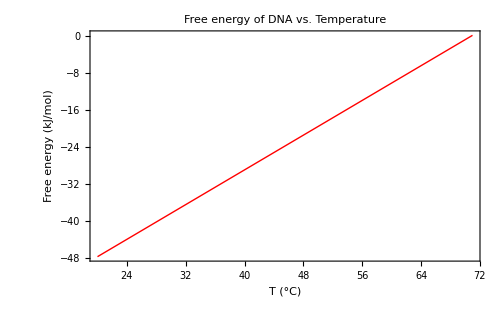

```mathematica
Plot[10^-3 ΔFdna[(T+273.15) Quantity[1,"Kelvins"]],{T,20,71},PlotLabel->"Free energy of DNA vs. Temperature",FrameLabel->{"T (°C)","Free energy (kJ/mol)"}]
```

Temperature at which the attraction between DNA strands becomes attractive. Below this temperature ΔFdna is negative.

```mathematica
T0=UnitConvert[ΔHdna/ΔSdna,"DegreesCelsius"]//N
```

70.8671 °C

```mathematica
ΔHdna-UnitConvert[T0] ΔSdna
```

0. J/mol

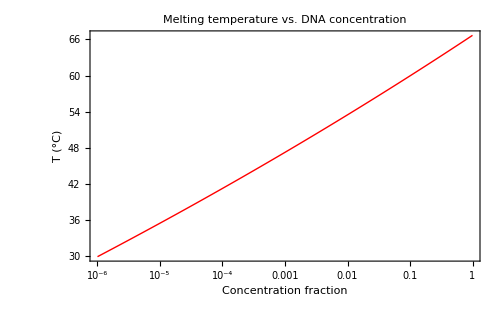

```mathematica
Tm[c_]=ΔHdna/(ΔSdna+R Log[c/4])//N;
LogLinearPlot[Tm[c]-Quantity[273.15,"Kelvins"],{c,10^-6,1},PlotRange->All,PlotLabel->"Melting temperature vs. DNA concentration",FrameLabel->{"Concentration fraction","T (°C)"}]
```

```mathematica
ρ=Quantity[6.4 10^3,1/("Micrometers")^2];
Rparticle=Quantity[525,"Nanometers"];
L=Quantity[15,"Nanometers"];
h=Quantity[15,"Nanometers"];
Nbonds[χ_]=2π χ ρ Rparticle^2(L-h/2)/(Rparticle+L) (*ref 24*)
2π Rparticle/L(L-h)^2 ρ (*ref 20, with L=20 and h=13±5*)
```

153.938 χ

0.

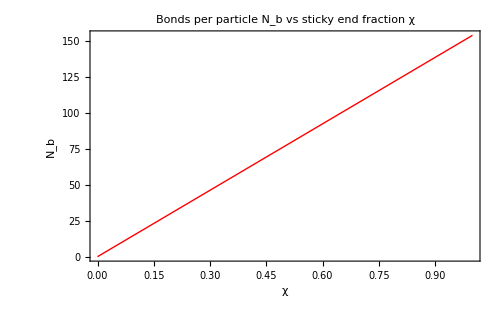

```mathematica
Plot[Nbonds[χ],{χ,0,1},PlotLabel->"Bonds per particle N_b vs sticky end fraction χ",FrameLabel->{"χ","N_b"}]
```

The dissociation temperature

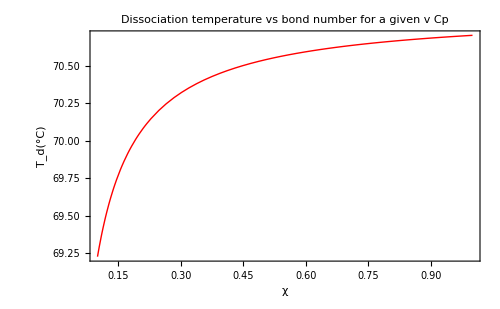

```mathematica
Td=ΔHdna/(ΔSdna+R Log[v Cp/4]/Nbonds[χ]);
Plot[(Td/.{v->1,Cp->0.001})-Quantity[273.15,"Kelvins"],{χ,0.1,1},PlotLabel->"Dissociation temperature vs bond number\nfor a given v Cp",FrameLabel->{"χ","T_d(°C)"}]
```

The width of the dissociation transition
“The dissociation curves are much sharper, 2δT =1 °C. See ref24.fig2.

(Log[(Cp v)/2] (-1.11739 K R))/(χ (-936 J/(K mol)+(Log[(Cp v)/4] (0.00649612 R))/χ))

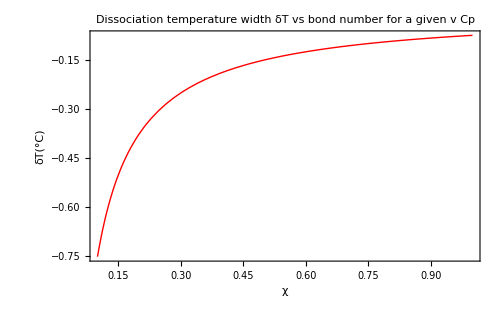

```mathematica
δT=-1/2(R Td Log[v Cp/2])/(Nbonds[χ] ΔSdna)
Plot[UnitConvert[(δT/.{v->1,Cp->0.001})],{χ,0.1,1},PlotLabel->"Dissociation temperature width δT vs bond number\nfor a given v Cp",FrameLabel->{"χ","δT(°C)"},PlotRange->All]
```

Experimentally we see that the dissociation temperature is far below 70°C. Why? ref24.fig3 shows that hybridized tethers have far fewer possible states. Thus there is a configurational entropy cost

I don’t understand this formula:

```mathematica
ΔSp=-10 R ;
```

Number of complementary strands that each sticky end can bind to on the opposite particle surface

```mathematica
k=3π L^2 ρ χ
```

13.5717 χ

```mathematica
ΔFtether[T_]=ΔFdna[T]-T ΔSp;
```

The partition function for two interacting DNA coated bead surfaces:

```mathematica
Zs=(1+k Exp[(-ΔFtether[T])/(kB T)])^Nbonds[χ]
```

(1+13.5717 ⅇ^(((-1 /k) (-322 kJ/mol+T (10 R)+T (936 J/(K mol))))/T) χ)^(153.938 χ)

Particle binding free energy

```mathematica
ΔFbead[T_]=-R T Log[Zs]
```

T Log[(1+13.5717 ⅇ^(((-1 /k) (-322 kJ/mol+T (10 R)+T (936 J/(K mol))))/T) χ)^(153.938 χ)] (-1 R)

Experimentally the particles don’t pair up, but form fractal like aggregates with coordination number z=3

Ap is the area a particle can move wiithout losiing the attractive interaction with its neighbors. Square well model, δ is the length of the tsticky ennd.

```mathematica
Ap=(δ/2)^2/.δ-> Quantity[3.6,"Nanometers"];
```

```mathematica
μ[χ_]=(z/2 ΔFbead[T]- R T Log[Ap])/.z->3;
```

Equilibrium constant

```mathematica
K=(δ/2)^2 Exp[(-ΔFbead[T])/(kB T 2)]
```

1/4 δ^2 ((1+13.5717 ⅇ^(((-1 /k) (-322 kJ/mol+T (10 R)+T (936 J/(K mol))))/T) χ)^(153.938 χ))^(1/2 R/k)

Singlet fraction

```mathematica
f=(1+2 K Cp -√(1+4 K Cp))/(2(K Cp)^2);
```

```mathematica
T0Tether=UnitConvert[ΔHdna/(ΔSdna+ΔSp),"DegreesCelsius"]//N
```

42.8012 °C

```mathematica
LTether=Quantity[15,"Nanometers"];
hTether=Quantity[21,"Nanometers"];
NbondsTether[χ_]=2π χ ρ Rparticle^2(LTether-hTether/2)/(Rparticle+L) (*ref 24*)
```

92.3628 χ

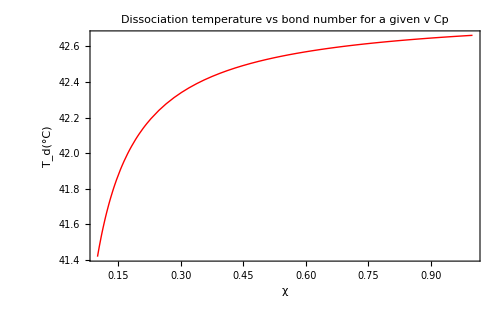

```mathematica
TdTether=ΔHdna/(ΔSdna+ΔSp+R Log[v Cp/4]/Nbonds[χ]);
Plot[(TdTether/.{v->1,Cp->0.001})-Quantity[273.15,"Kelvins"],{χ,0.1,1},PlotLabel->"Dissociation temperature vs bond number\nfor a given v Cp",FrameLabel->{"χ","T_d(°C)"}]
```